### Set Options

Automating good looking plots

```mathematica
SetOptions[ DiscretePlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
SetOptions[ ListPlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium,PlotStyle->{Black,Thick}];
```

```mathematica
SetOptions[ ListContourPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium]; SetOptions[ ListDensityPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
```

```mathematica
SetOptions[ ContourPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium]; SetOptions[ DensityPlot,Frame-> True,LabelStyle->{FontFamily->"CMU Serif",FontSize->24,Black},ImageSize->Medium];
```

### Parameters

Lattice vectors, and basis vectors

```mathematica
a1 = {1,0};a2 ={0,1};τA = {1/2,0};τB = {0,0}; τC = {0,1/2};τvec = {τA,τB, τC};
```

Reciprocal lattice vectors

```mathematica
LatMat = {a1,a2}; 
ReciLatMat = 2π Inverse[LatMat]†;
b1 = ReciLatMat[[1]] ;b2 = ReciLatMat[[2]];
```

```mathematica
δf=N[1/(2√2)];
```

kSpan : set of points for k-sums, and rSpan : set of points for r-sums

```mathematica
kSpan[krange_]:=N[Flatten[Table[i*b1+j*b2,{i,0,0.999,1/krange},{j,0,0.999,1/krange}],1]];
```

```mathematica
rSpan[range_]:=N[Flatten[Table[i*a1+j*a2,{i,-range,range},{j,-range,range}],1]];
```

```mathematica
inp[a_,b_]:= Conjugate[a].b;
```

We will play around with k-range and range to check for convergence

### Bloch Hamiltonian

```mathematica
ak[δ_,k_] := N[Cos[k/2] + I δ Sin[k/2]]; akc[δ_,k_] :=N[ Cos[k/2] - I δ Sin[k/2]];
```

```mathematica
bk[k_]:= N[ Cos[(k.(a1+a2))/2] +Cos[(k.(a1-a2))/2] ];
```

```mathematica
Clear[hamLiebG2];hamLiebG2[tp_,δ_,k_] := hamLiebG2[tp,δ,k] = 2{{ 0, ak[δ,k[[1]]],tp bk[k]},{akc[δ,k[[1]]] ,0,ak[δ,k[[2]]] },{tp bk[k], akc[δ,k[[2]]] ,0}};
```

```mathematica
Clear[EnerLiebG2];EnerLiebG2[tp_,δ_,k_] := EnerLiebG2[tp,δ,k]= Chop[  N[Sort[Eigenvalues[hamLiebG2[tp,δ,k]]]] ];
Clear[ULiebG2];ULiebG2[tp_,δ_,k_] :=ULiebG2[tp,δ,k]=Transpose[Chop[N[   Transpose[ SortBy[ Transpose[ Eigensystem[ hamLiebG2[tp,δ,k] ] ] ,First ] ][[2]] ] ] ] ;
```

```mathematica
Clear[MassInv];MassInv[tp_,δ_,k_,dn_] := MassInv[tp,δ,k,dn] = Module[ {u =ULiebG2[tp,δ,k], D2h = 1/dn^2(hamLiebG2[tp,δ,k+{dn,0}] +hamLiebG2[tp,δ,k-{dn,0}]-2hamLiebG2[tp,δ,k])},u†.D2h.u];
```

```mathematica
Fermi[β_,x_]:=Chop[N[ 1/(1+ Exp[ β x])]];
```

```mathematica
Clear[Dtilde];Dtilde[tp_,δ_,dn_,μ_,β_,krange_] := Dtilde[tp,δ,dn,μ,β,krange] = 1/Length[kSpan[krange]] Sum[ MassInv[tp,δ,k,dn] [[band,band]] Fermi[β, EnerLiebG2[tp,δ,k][[band]]-μ],{k,kSpan[krange]},{band,1,3}];
```

```mathematica
Clear[Midμ];Midμ[tp_,δ_,dn_,krange_] := Midμ[tp,δ,dn,krange] =1/2( Max[ Table[ EnerLiebG2[tp,δ,k][[1]],{k,kSpan[krange]}]]+Min[ Table[ EnerLiebG2[tp,δ,k][[2]],{k,kSpan[krange]}]]);
```

```mathematica
Clear[FlatNess];FlatNess[tvec_,Δ_,dn_,krange_] := FlatNess[tvec,Δ,dn,krange] =  Max[ Table[ EnerLiebG2[tvec,Δ,k][[2]],{k,kSpan[krange]}]]-Min[ Table[ EnerLiebG2[tvec,Δ,k][[2]],{k,kSpan[krange]}]]
```

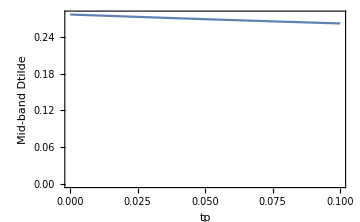

```mathematica
Block[ {δ=0.5, dn=0.01, β=1000,krange=20}, DiscretePlot[ Re[Dtilde[tp,δ,dn,Midμ[tp,δ,dn,krange],β,krange]] ,{tp,0.0,0.1,0.01},FrameLabel->{"tp","Mid-band Dtilde"},PlotRange->{0,Automatic}]]
```

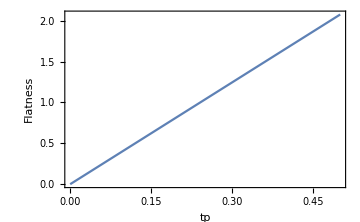

```mathematica
Block[ {δ=0.5, dn=0.01, β=1000,krange=20}, DiscretePlot[ FlatNess[tp,δ,dn,krange],{tp,0.0,0.5,0.1},PlotRange->All,FrameLabel->{"tp","Flatness"}]]
```